# Runtime Testing

```mathematica
<<StoChemSim`
```

## Direct SSA

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSysSSA[construction_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,totalTime,runtimeInfo,totalTimePerIter,algoTimePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[ExpandRevrxns[rxns]];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
totalTimePerIter=totalTime/iters;
runtimeInfo=GetRuntimeInfo[];
out={construction,statesOnlyFlag,nRxns,nSpecies,iters,totalTime,totalTimePerIter,runtimeInfo};
Print[out];
out],
{k,kRange}]]
```

## Constructions 1, 2, and 3 up to 200 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
kRange={1,3,5,10};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→7.1×10^-6,backend→0.113995|>}

{ConstructSys1,False,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000175,backend→0.228378|>}

{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.015625,interface→0.0000708,backend→0.461003|>}

{ConstructSys1,False,200,200,100000,1.6875,0.000016875,<|frontend→0.03125,interface→0.000265,backend→1.65992|>}

{ConstructSys1,True,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→5.×10^-6,backend→0.105245|>}

{ConstructSys1,True,18,18,100000,0.25,2.5×10^-6,<|frontend→0.,interface→0.0000202,backend→0.249933|>}

{ConstructSys1,True,50,50,100000,0.46875,4.6875×10^-6,<|frontend→0.,interface→0.0000456,backend→0.469555|>}

{ConstructSys1,True,200,200,100000,1.65625,0.0000165625,<|frontend→0.015625,interface→0.0009718,backend→1.64295|>}

{ConstructSys2,False,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→9.×10^-6,backend→0.114242|>}

{ConstructSys2,False,18,18,100000,0.609375,6.09375×10^-6,<|frontend→0.015625,interface→0.0000353,backend→0.60596|>}

{ConstructSys2,False,50,50,100000,1.51563,0.0000151563,<|frontend→0.,interface→0.0001274,backend→1.525|>}

{ConstructSys2,False,200,200,100000,4.39063,0.0000439063,<|frontend→0.078125,interface→0.0007522,backend→4.32253|>}

{ConstructSys2,True,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→9.4×10^-6,backend→0.107083|>}

{ConstructSys2,True,18,18,100000,0.5625,5.625×10^-6,<|frontend→0.,interface→0.0000348,backend→0.572192|>}

{ConstructSys2,True,50,50,100000,1.35938,0.0000135938,<|frontend→0.,interface→0.0001648,backend→1.35917|>}

{ConstructSys2,True,200,200,100000,4.89063,0.0000489063,<|frontend→0.0625,interface→0.0004199,backend→4.8287|>}

{ConstructSys3,False,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→6.3×10^-6,backend→0.106698|>}

{ConstructSys3,False,18,18,100000,0.84375,8.4375×10^-6,<|frontend→0.,interface→0.000037,backend→0.830364|>}

{ConstructSys3,False,50,50,100000,2.42188,0.0000242188,<|frontend→0.03125,interface→0.0003615,backend→2.39013|>}

{ConstructSys3,False,200,200,100000,16.125,0.00016125,<|frontend→0.21875,interface→0.0014882,backend→16.0543|>}

{ConstructSys3,True,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.015625,interface→7.4×10^-6,backend→0.10427|>}

{ConstructSys3,True,18,18,100000,1.17188,0.0000117188,<|frontend→0.015625,interface→0.000041,backend→1.15956|>}

{ConstructSys3,True,50,50,100000,2.51563,0.0000251563,<|frontend→0.015625,interface→0.0001464,backend→2.51695|>}

{ConstructSys3,True,200,200,100000,16.0313,0.000160313,<|frontend→0.203125,interface→0.001017,backend→15.9023|>}

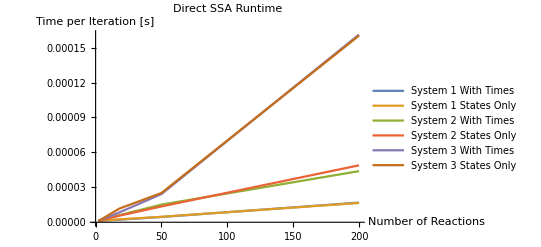

```mathematica
coorsSSA=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem], resultsSSA];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem], coorsSSA];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→7.1×10^-6,backend→0.113995|>},{ConstructSys1,False,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000175,backend→0.228378|>},{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.015625,interface→0.0000708,backend→0.461003|>},{ConstructSys1,False,200,200,100000,1.6875,0.000016875,<|frontend→0.03125,interface→0.000265,backend→1.65992|>}},{{ConstructSys1,True,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→5.×10^-6,backend→0.105245|>},{ConstructSys1,True,18,18,100000,0.25,2.5×10^-6,<|frontend→0.,interface→0.0000202,backend→0.249933|>},{ConstructSys1,True,50,50,100000,0.46875,4.6875×10^-6,<|frontend→0.,interface→0.0000456,backend→0.469555|>},{ConstructSys1,True,200,200,100000,1.65625,0.0000165625,<|frontend→0.015625,interface→0.0009718,backend→1.64295|>}}},{{{ConstructSys2,False,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→9.×10^-6,backend→0.114242|>},{ConstructSys2,False,18,18,100000,0.609375,6.09375×10^-6,<|frontend→0.015625,interface→0.0000353,backend→0.60596|>},{ConstructSys2,False,50,50,100000,1.51563,0.0000151563,<|frontend→0.,interface→0.0001274,backend→1.525|>},{ConstructSys2,False,200,200,100000,4.39063,0.0000439063,<|frontend→0.078125,interface→0.0007522,backend→4.32253|>}},{{ConstructSys2,True,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→9.4×10^-6,backend→0.107083|>},{ConstructSys2,True,18,18,100000,0.5625,5.625×10^-6,<|frontend→0.,interface→0.0000348,backend→0.572192|>},{ConstructSys2,True,50,50,100000,1.35938,0.0000135938,<|frontend→0.,interface→0.0001648,backend→1.35917|>},{ConstructSys2,True,200,200,100000,4.89063,0.0000489063,<|frontend→0.0625,interface→0.0004199,backend→4.8287|>}}},{{{ConstructSys3,False,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→6.3×10^-6,backend→0.106698|>},{ConstructSys3,False,18,18,100000,0.84375,8.4375×10^-6,<|frontend→0.,interface→0.000037,backend→0.830364|>},{ConstructSys3,False,50,50,100000,2.42188,0.0000242188,<|frontend→0.03125,interface→0.0003615,backend→2.39013|>},{ConstructSys3,False,200,200,100000,16.125,0.00016125,<|frontend→0.21875,interface→0.0014882,backend→16.0543|>}},{{ConstructSys3,True,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.015625,interface→7.4×10^-6,backend→0.10427|>},{ConstructSys3,True,18,18,100000,1.17188,0.0000117188,<|frontend→0.015625,interface→0.000041,backend→1.15956|>},{ConstructSys3,True,50,50,100000,2.51563,0.0000251563,<|frontend→0.015625,interface→0.0001464,backend→2.51695|>},{ConstructSys3,True,200,200,100000,16.0313,0.000160313,<|frontend→0.203125,interface→0.001017,backend→15.9023|>}}}}

{{{2,1.25×10^-6},{18,2.1875×10^-6},{50,4.53125×10^-6},{200,0.000016875}},{{2,1.09375×10^-6},{18,2.5×10^-6},{50,4.6875×10^-6},{200,0.0000165625}},{{2,1.09375×10^-6},{18,6.09375×10^-6},{50,0.0000151563},{200,0.0000439063}},{{2,1.09375×10^-6},{18,5.625×10^-6},{50,0.0000135938},{200,0.0000489063}},{{2,1.09375×10^-6},{18,8.4375×10^-6},{50,0.0000242188},{200,0.00016125}},{{2,9.375×10^-7},{18,0.0000117188},{50,0.0000251563},{200,0.000160313}}}

## Constructions 1 and 2 up to 1,250 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2};
kRange={1,3,5,10,25};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA2=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→0.0000175,backend→0.102602|>}

{ConstructSys1,False,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000265,backend→0.236695|>}

{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.015625,interface→0.0000426,backend→0.44274|>}

{ConstructSys1,False,200,200,100000,1.51563,0.0000151563,<|frontend→0.03125,interface→0.0001405,backend→1.48307|>}

{ConstructSys1,False,1250,1250,100000,9.48438,0.0000948438,<|frontend→0.3125,interface→0.0022155,backend→9.32677|>}

{ConstructSys1,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→6.6×10^-6,backend→0.140391|>}

{ConstructSys1,True,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000328,backend→0.318762|>}

{ConstructSys1,True,50,50,100000,0.609375,6.09375×10^-6,<|frontend→0.,interface→0.0000498,backend→0.605765|>}

{ConstructSys1,True,200,200,100000,1.64063,0.0000164063,<|frontend→0.03125,interface→0.0002916,backend→1.64922|>}

{ConstructSys1,True,1250,1250,100000,10.2813,0.000102813,<|frontend→0.34375,interface→0.0047454,backend→10.2465|>}

{ConstructSys2,False,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→7.×10^-6,backend→0.10998|>}

{ConstructSys2,False,18,18,100000,0.609375,6.09375×10^-6,<|frontend→0.,interface→0.0000733,backend→0.61149|>}

{ConstructSys2,False,50,50,100000,1.32813,0.0000132813,<|frontend→0.,interface→0.0000985,backend→1.32895|>}

{ConstructSys2,False,200,200,100000,4.09375,0.0000409375,<|frontend→0.046875,interface→0.0004131,backend→4.03976|>}

{ConstructSys2,False,1250,1250,100000,27.7656,0.000277656,<|frontend→0.96875,interface→0.0097324,backend→26.9843|>}

{ConstructSys2,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.03125,interface→6.9×10^-6,backend→0.0959495|>}

{ConstructSys2,True,18,18,100000,0.8125,8.125×10^-6,<|frontend→0.015625,interface→0.0000322,backend→0.797806|>}

{ConstructSys2,True,50,50,100000,1.34375,0.0000134375,<|frontend→0.015625,interface→0.0001075,backend→1.33483|>}

{ConstructSys2,True,200,200,100000,4.35938,0.0000435938,<|frontend→0.0625,interface→0.0004257,backend→4.28635|>}

{ConstructSys2,True,1250,1250,100000,26.3438,0.000263438,<|frontend→0.953125,interface→0.0054313,backend→25.4256|>}

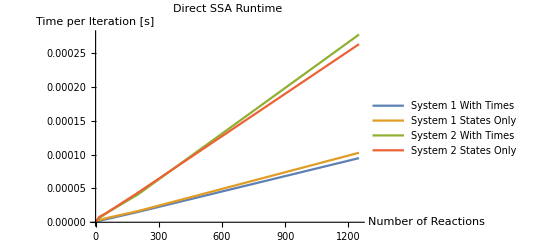

```mathematica
coorsSSA2=Flatten[Table[
Table[{resultsSSA2[[i]][[j]][[l]][[3]],resultsSSA2[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA2[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA2,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem], resultsSSA2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem], coorsSSA2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→0.0000175,backend→0.102602|>},{ConstructSys1,False,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000265,backend→0.236695|>},{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.015625,interface→0.0000426,backend→0.44274|>},{ConstructSys1,False,200,200,100000,1.51563,0.0000151563,<|frontend→0.03125,interface→0.0001405,backend→1.48307|>},{ConstructSys1,False,1250,1250,100000,9.48438,0.0000948438,<|frontend→0.3125,interface→0.0022155,backend→9.32677|>}},{{ConstructSys1,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→6.6×10^-6,backend→0.140391|>},{ConstructSys1,True,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000328,backend→0.318762|>},{ConstructSys1,True,50,50,100000,0.609375,6.09375×10^-6,<|frontend→0.,interface→0.0000498,backend→0.605765|>},{ConstructSys1,True,200,200,100000,1.64063,0.0000164063,<|frontend→0.03125,interface→0.0002916,backend→1.64922|>},{ConstructSys1,True,1250,1250,100000,10.2813,0.000102813,<|frontend→0.34375,interface→0.0047454,backend→10.2465|>}}},{{{ConstructSys2,False,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→7.×10^-6,backend→0.10998|>},{ConstructSys2,False,18,18,100000,0.609375,6.09375×10^-6,<|frontend→0.,interface→0.0000733,backend→0.61149|>},{ConstructSys2,False,50,50,100000,1.32813,0.0000132813,<|frontend→0.,interface→0.0000985,backend→1.32895|>},{ConstructSys2,False,200,200,100000,4.09375,0.0000409375,<|frontend→0.046875,interface→0.0004131,backend→4.03976|>},{ConstructSys2,False,1250,1250,100000,27.7656,0.000277656,<|frontend→0.96875,interface→0.0097324,backend→26.9843|>}},{{ConstructSys2,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.03125,interface→6.9×10^-6,backend→0.0959495|>},{ConstructSys2,True,18,18,100000,0.8125,8.125×10^-6,<|frontend→0.015625,interface→0.0000322,backend→0.797806|>},{ConstructSys2,True,50,50,100000,1.34375,0.0000134375,<|frontend→0.015625,interface→0.0001075,backend→1.33483|>},{ConstructSys2,True,200,200,100000,4.35938,0.0000435938,<|frontend→0.0625,interface→0.0004257,backend→4.28635|>},{ConstructSys2,True,1250,1250,100000,26.3438,0.000263438,<|frontend→0.953125,interface→0.0054313,backend→25.4256|>}}}}

{{{2,1.09375×10^-6},{18,2.1875×10^-6},{50,4.53125×10^-6},{200,0.0000151563},{1250,0.0000948438}},{{2,1.25×10^-6},{18,3.125×10^-6},{50,6.09375×10^-6},{200,0.0000164063},{1250,0.000102813}},{{2,9.375×10^-7},{18,6.09375×10^-6},{50,0.0000132813},{200,0.0000409375},{1250,0.000277656}},{{2,1.25×10^-6},{18,8.125×10^-6},{50,0.0000134375},{200,0.0000435938},{1250,0.000263438}}}

## Construction 1 up to 20,000 reactions

```mathematica
constructions={ConstructSys1};
kRange={1,3,5,10,25,50,100};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA3=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.03125,interface→6.8×10^-6,backend→0.099433|>}

{ConstructSys1,False,18,18,100000,0.234375,2.34375×10^-6,<|frontend→0.015625,interface→0.0000271,backend→0.223627|>}

{ConstructSys1,False,50,50,100000,0.421875,4.21875×10^-6,<|frontend→0.,interface→0.000077,backend→0.431442|>}

{ConstructSys1,False,200,200,100000,1.45313,0.0000145313,<|frontend→0.03125,interface→0.0002703,backend→1.42279|>}

{ConstructSys1,False,1250,1250,100000,8.89063,0.0000889063,<|frontend→0.3125,interface→0.002362,backend→8.58304|>}

{ConstructSys1,False,5000,5000,100000,45.6875,0.000456875,<|frontend→4.07813,interface→0.0332802,backend→41.7218|>}

{ConstructSys1,False,20000,20000,100000,259.656,0.00259656,<|frontend→63.0156,interface→0.903033,backend→197.71|>}

{ConstructSys1,True,2,2,100000,0.140625,1.40625×10^-6,<|frontend→0.015625,interface→7.3×10^-6,backend→0.120945|>}

{ConstructSys1,True,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000446,backend→0.322377|>}

{ConstructSys1,True,50,50,100000,0.609375,6.09375×10^-6,<|frontend→0.015625,interface→0.0001127,backend→0.592063|>}

{ConstructSys1,True,200,200,100000,1.75,0.0000175,<|frontend→0.046875,interface→0.0002786,backend→1.70871|>}

{ConstructSys1,True,1250,1250,100000,9.9375,0.000099375,<|frontend→0.390625,interface→0.0035989,backend→9.5418|>}

{ConstructSys1,True,5000,5000,100000,46.1563,0.000461563,<|frontend→4.42188,interface→0.0495316,backend→41.6309|>}

{ConstructSys1,True,20000,20000,100000,297.531,0.00297531,<|frontend→68.6094,interface→1.08,backend→241.722|>}

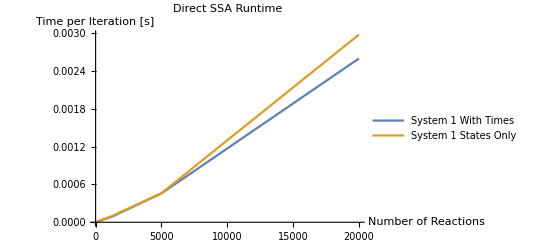

```mathematica
coorsSSA3=Flatten[Table[
Table[{resultsSSA3[[i]][[j]][[l]][[3]],resultsSSA3[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA3[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA3,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem], resultsSSA3];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem], coorsSSA3];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.03125,interface→6.8×10^-6,backend→0.099433|>},{ConstructSys1,False,18,18,100000,0.234375,2.34375×10^-6,<|frontend→0.015625,interface→0.0000271,backend→0.223627|>},{ConstructSys1,False,50,50,100000,0.421875,4.21875×10^-6,<|frontend→0.,interface→0.000077,backend→0.431442|>},{ConstructSys1,False,200,200,100000,1.45313,0.0000145313,<|frontend→0.03125,interface→0.0002703,backend→1.42279|>},{ConstructSys1,False,1250,1250,100000,8.89063,0.0000889063,<|frontend→0.3125,interface→0.002362,backend→8.58304|>},{ConstructSys1,False,5000,5000,100000,45.6875,0.000456875,<|frontend→4.07813,interface→0.0332802,backend→41.7218|>},{ConstructSys1,False,20000,20000,100000,259.656,0.00259656,<|frontend→63.0156,interface→0.903033,backend→197.71|>}},{{ConstructSys1,True,2,2,100000,0.140625,1.40625×10^-6,<|frontend→0.015625,interface→7.3×10^-6,backend→0.120945|>},{ConstructSys1,True,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000446,backend→0.322377|>},{ConstructSys1,True,50,50,100000,0.609375,6.09375×10^-6,<|frontend→0.015625,interface→0.0001127,backend→0.592063|>},{ConstructSys1,True,200,200,100000,1.75,0.0000175,<|frontend→0.046875,interface→0.0002786,backend→1.70871|>},{ConstructSys1,True,1250,1250,100000,9.9375,0.000099375,<|frontend→0.390625,interface→0.0035989,backend→9.5418|>},{ConstructSys1,True,5000,5000,100000,46.1563,0.000461563,<|frontend→4.42188,interface→0.0495316,backend→41.6309|>},{ConstructSys1,True,20000,20000,100000,297.531,0.00297531,<|frontend→68.6094,interface→1.08,backend→241.722|>}}}}

{{{2,1.25×10^-6},{18,2.34375×10^-6},{50,4.21875×10^-6},{200,0.0000145313},{1250,0.0000889063},{5000,0.000456875},{20000,0.00259656}},{{2,1.40625×10^-6},{18,3.125×10^-6},{50,6.09375×10^-6},{200,0.0000175},{1250,0.000099375},{5000,0.000461563},{20000,0.00297531}}}

## Bounded Tau Leaping

```mathematica
<<StoChemSim`
```

```mathematica
ConstructSysMax[n_]:={
rxnl[{x1},{y,z1},1],
rxnl[{x2},{y,z2},1],
rxnl[{z1,z2},{k},1/n],
rxnl[{k,y},{},1/n],
conc[{x1,x2},n/2]
};
```

```mathematica
TestSysBTL[construction_,simulation_,nRange_]:=Module[{},
Table[Module[
{rxnsys,results,totalTime,runtimeInfo,algoTime},
rxnsys= construction[n];
results=Timing[simulation[rxnsys,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
out={simulation,n,totalTime,runtimeInfo};
Print[out];
out],
{n,nRange}]]
```

## Direct SSA vs. BTL up to 32,768 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[2^i,{i,1,15}];
resultsBTL=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,2,0.015625,<|frontend→0.015625,interface→0.000016,backend→0.0012471|>}

{SimulateDirectSSA,4,0.,<|frontend→0.,interface→9.7×10^-6,backend→0.0004594|>}

{SimulateDirectSSA,8,0.,<|frontend→0.,interface→5.8×10^-6,backend→0.000866|>}

{SimulateDirectSSA,16,0.,<|frontend→0.,interface→5.1×10^-6,backend→0.0000602|>}

{SimulateDirectSSA,32,0.,<|frontend→0.,interface→4.7×10^-6,backend→0.0001293|>}

{SimulateDirectSSA,64,0.015625,<|frontend→0.,interface→6.8×10^-6,backend→0.0001623|>}

{SimulateDirectSSA,128,0.,<|frontend→0.,interface→8.8×10^-6,backend→0.0004091|>}

{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.4×10^-6,backend→0.0006556|>}

{SimulateDirectSSA,512,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0013157|>}

{SimulateDirectSSA,1024,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.004772|>}

{SimulateDirectSSA,2048,0.015625,<|frontend→0.,interface→6.2×10^-6,backend→0.0057106|>}

{SimulateDirectSSA,4096,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.0113347|>}

{SimulateDirectSSA,8192,0.03125,<|frontend→0.,interface→8.1×10^-6,backend→0.0216833|>}

{SimulateDirectSSA,16384,0.046875,<|frontend→0.,interface→0.0000183,backend→0.0440275|>}

{SimulateDirectSSA,32768,0.078125,<|frontend→0.,interface→6.1×10^-6,backend→0.0878965|>}

{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→6.6×10^-6,backend→0.0009589|>}

{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0001275|>}

{SimulateBoundedTauLeaping,8,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0002533|>}

{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→0.0000289,backend→0.0006843|>}

{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→8.5×10^-6,backend→0.000947|>}

{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0019396|>}

{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0036934|>}

{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.,interface→7.1×10^-6,backend→0.0076757|>}

{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→5.5×10^-6,backend→0.0114099|>}

{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→5.7×10^-6,backend→0.0170177|>}

{SimulateBoundedTauLeaping,2048,0.015625,<|frontend→0.,interface→9.5×10^-6,backend→0.0232597|>}

{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→5.6×10^-6,backend→0.0292565|>}

{SimulateBoundedTauLeaping,8192,0.03125,<|frontend→0.,interface→8.2×10^-6,backend→0.0336564|>}

{SimulateBoundedTauLeaping,16384,0.0625,<|frontend→0.,interface→6.1×10^-6,backend→0.0488705|>}

{SimulateBoundedTauLeaping,32768,0.0625,<|frontend→0.,interface→5.9×10^-6,backend→0.0683247|>}

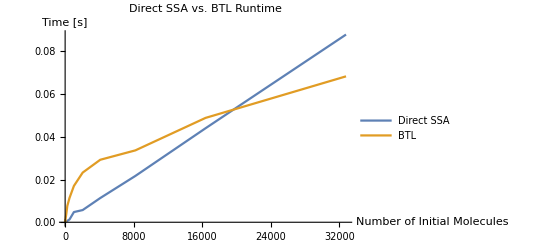

```mathematica
coorsBTL=Table[
Table[{resultsBTL[[i]][[l]][[2]],resultsBTL[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem], resultsBTL];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem], coorsBTL];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,2,0.015625,<|frontend→0.015625,interface→0.000016,backend→0.0012471|>},{SimulateDirectSSA,4,0.,<|frontend→0.,interface→9.7×10^-6,backend→0.0004594|>},{SimulateDirectSSA,8,0.,<|frontend→0.,interface→5.8×10^-6,backend→0.000866|>},{SimulateDirectSSA,16,0.,<|frontend→0.,interface→5.1×10^-6,backend→0.0000602|>},{SimulateDirectSSA,32,0.,<|frontend→0.,interface→4.7×10^-6,backend→0.0001293|>},{SimulateDirectSSA,64,0.015625,<|frontend→0.,interface→6.8×10^-6,backend→0.0001623|>},{SimulateDirectSSA,128,0.,<|frontend→0.,interface→8.8×10^-6,backend→0.0004091|>},{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.4×10^-6,backend→0.0006556|>},{SimulateDirectSSA,512,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0013157|>},{SimulateDirectSSA,1024,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.004772|>},{SimulateDirectSSA,2048,0.015625,<|frontend→0.,interface→6.2×10^-6,backend→0.0057106|>},{SimulateDirectSSA,4096,0.,<|frontend→0.,interface→7.8×10^-6,backend→0.0113347|>},{SimulateDirectSSA,8192,0.03125,<|frontend→0.,interface→8.1×10^-6,backend→0.0216833|>},{SimulateDirectSSA,16384,0.046875,<|frontend→0.,interface→0.0000183,backend→0.0440275|>},{SimulateDirectSSA,32768,0.078125,<|frontend→0.,interface→6.1×10^-6,backend→0.0878965|>}},{{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→6.6×10^-6,backend→0.0009589|>},{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0001275|>},{SimulateBoundedTauLeaping,8,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0002533|>},{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→0.0000289,backend→0.0006843|>},{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→8.5×10^-6,backend→0.000947|>},{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→7.2×10^-6,backend→0.0019396|>},{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0036934|>},{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.,interface→7.1×10^-6,backend→0.0076757|>},{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→5.5×10^-6,backend→0.0114099|>},{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→5.7×10^-6,backend→0.0170177|>},{SimulateBoundedTauLeaping,2048,0.015625,<|frontend→0.,interface→9.5×10^-6,backend→0.0232597|>},{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→5.6×10^-6,backend→0.0292565|>},{SimulateBoundedTauLeaping,8192,0.03125,<|frontend→0.,interface→8.2×10^-6,backend→0.0336564|>},{SimulateBoundedTauLeaping,16384,0.0625,<|frontend→0.,interface→6.1×10^-6,backend→0.0488705|>},{SimulateBoundedTauLeaping,32768,0.0625,<|frontend→0.,interface→5.9×10^-6,backend→0.0683247|>}}}

{{{2,0.0012471},{4,0.0004594},{8,0.000866},{16,0.0000602},{32,0.0001293},{64,0.0001623},{128,0.0004091},{256,0.0006556},{512,0.0013157},{1024,0.004772},{2048,0.0057106},{4096,0.0113347},{8192,0.0216833},{16384,0.0440275},{32768,0.0878965}},{{2,0.0009589},{4,0.0001275},{8,0.0002533},{16,0.0006843},{32,0.000947},{64,0.0019396},{128,0.0036934},{256,0.0076757},{512,0.0114099},{1024,0.0170177},{2048,0.0232597},{4096,0.0292565},{8192,0.0336564},{16384,0.0488705},{32768,0.0683247}}}

## Direct SSA vs. BTL up to 1,000,000 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[10^i,{i,1,6}];
resultsBTL2=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,10,0.,<|frontend→0.,interface→8.4×10^-6,backend→0.0001028|>}

{SimulateDirectSSA,100,0.,<|frontend→0.,interface→4.9×10^-6,backend→0.0002795|>}

{SimulateDirectSSA,1000,0.,<|frontend→0.,interface→4.8×10^-6,backend→0.0024228|>}

{SimulateDirectSSA,10000,0.03125,<|frontend→0.,interface→6.9×10^-6,backend→0.0315906|>}

{SimulateDirectSSA,100000,0.265625,<|frontend→0.,interface→8.6×10^-6,backend→0.25897|>}

{SimulateDirectSSA,1000000,2.39063,<|frontend→0.,interface→9.9×10^-6,backend→2.41952|>}

{SimulateBoundedTauLeaping,10,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.000269|>}

{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0027333|>}

{SimulateBoundedTauLeaping,1000,0.015625,<|frontend→0.,interface→6.9×10^-6,backend→0.016234|>}

{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→5.7×10^-6,backend→0.035583|>}

{SimulateBoundedTauLeaping,100000,0.09375,<|frontend→0.,interface→8.7×10^-6,backend→0.0891383|>}

{SimulateBoundedTauLeaping,1000000,0.234375,<|frontend→0.,interface→7.×10^-6,backend→0.246433|>}

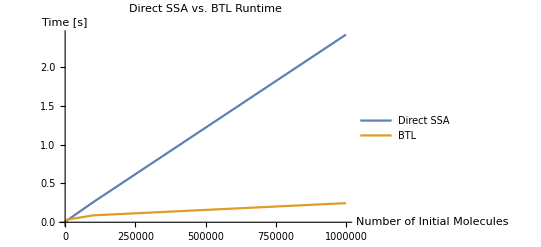

```mathematica
coorsBTL2=Table[
Table[{resultsBTL2[[i]][[l]][[2]],resultsBTL2[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL2[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL2,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem], resultsBTL2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem], coorsBTL2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,10,0.,<|frontend→0.,interface→8.4×10^-6,backend→0.0001028|>},{SimulateDirectSSA,100,0.,<|frontend→0.,interface→4.9×10^-6,backend→0.0002795|>},{SimulateDirectSSA,1000,0.,<|frontend→0.,interface→4.8×10^-6,backend→0.0024228|>},{SimulateDirectSSA,10000,0.03125,<|frontend→0.,interface→6.9×10^-6,backend→0.0315906|>},{SimulateDirectSSA,100000,0.265625,<|frontend→0.,interface→8.6×10^-6,backend→0.25897|>},{SimulateDirectSSA,1000000,2.39063,<|frontend→0.,interface→9.9×10^-6,backend→2.41952|>}},{{SimulateBoundedTauLeaping,10,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.000269|>},{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0027333|>},{SimulateBoundedTauLeaping,1000,0.015625,<|frontend→0.,interface→6.9×10^-6,backend→0.016234|>},{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→5.7×10^-6,backend→0.035583|>},{SimulateBoundedTauLeaping,100000,0.09375,<|frontend→0.,interface→8.7×10^-6,backend→0.0891383|>},{SimulateBoundedTauLeaping,1000000,0.234375,<|frontend→0.,interface→7.×10^-6,backend→0.246433|>}}}

{{{10,0.0001028},{100,0.0002795},{1000,0.0024228},{10000,0.0315906},{100000,0.25897},{1000000,2.41952}},{{10,0.000269},{100,0.0027333},{1000,0.016234},{10000,0.035583},{100000,0.0891383},{1000000,0.246433}}}